```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
```

```mathematica
Vtm12k2[ϕ_,G_]:=k^2 E^(2 ϕ/√6)(-12+4 √6 ϕ-3/2 ϕ^2+(√6)/4 ϕ G^2-3/2 G^2-1/16 G^4);
D[Vtm12k2[ϕ,G],G]==k^2 E^(2 ϕ/√6)((√6)/2 ϕ G-3G-1/4 G^3)//FullSimplify
D[Vtm12k2[ϕ,G],ϕ]==k^2 E^(2 ϕ/√6)(5ϕ-(√6)/2 ϕ^2+1/2 ϕ G^2-(√6)/4 G^2-(√6)/48 G^4)//FullSimplify
Vtm12k2scaled[ϕ_,G_]:=k^2(-12+4 √6 ϕ-3/2 ϕ^2+(√6)/4 ϕ G^2-3/2 G^2-1/16 G^4);
dVtdGscaled[ϕ_,G_]:=k^2((√6)/2 ϕ G-3G-1/4 G^3);
dVtdϕscaled[ϕ_,G_]:=k^2(5ϕ-(√6)/2 ϕ^2+1/2 ϕ G^2-(√6)/4 G^2-(√6)/48 G^4);
```

True

True

```mathematica
ϕ[x_]:=G[x]^2/(6 √6);
eq1=3 q x (f'[x]Df[x]+f[x](a Df[x] ϕ'[x]+Df'[x]))-12f[x] Df[x]^2==Vtm12k2scaled[ϕ[x],G[x]]/.a->1/(√6)//FullSimplify
eq2=Df'[x]+a ϕ'[x]Df[x]==1/6 q x(ϕ'[x]^2+G'[x]^2)/.a->1/(√6)//FullSimplify
eq3=(q^2 f[x](a x ϕ'[x]^2+ϕ'[x]+x ϕ''[x])+q^2 x f'[x]ϕ'[x]-4q f[x] Df[x] ϕ'[x])x==dVtdϕscaled[ϕ[x],G[x]]/.a->1/(√6)//FullSimplify
eq4=(q^2 f[x](a x ϕ'[x]G'[x]+G'[x]+x G''[x])+q^2 x f'[x]G'[x]-4q f[x] Df[x] G'[x])x==dVtdGscaled[ϕ[x],G[x]]/.a->1/(√6)//FullSimplify
```

432 Df[x]^2 f[x]==k^2 (432+30 G[x]^2+G[x]^4)+108 q x f[x] Df'[x]+6 q x Df[x] (18 f'[x]+f[x] G[x] G'[x])

324 Df'[x]==G'[x] (-18 Df[x] G[x]+q x (54+G[x]^2) G'[x])

3 k^2 G[x]^4+18 q^2 x^2 f[x] G'[x]^2+G[x]^2 (36 k^2+q^2 x^2 f[x] G'[x]^2)+18 q x G[x] (((q-4 Df[x]) f[x]+q x f'[x]) G'[x]+q x f[x] G''[x])==0

q x (q x f'[x] G'[x]+f[x] ((q-4 Df[x]) G'[x]+1/18 q x G[x] G'[x]^2+q x G''[x]))==-1/6 k^2 G[x] (18+G[x]^2)

```mathematica
simple=eq3[[1]]-18G[x]eq4[[1]]-eq3[[2]]+18G[x]eq4[[2]]==0//Expand
DSolve[simple,G[x],x]
Solve[simple,f[x]]
```

-18 k^2 G[x]^2+18 q^2 x^2 f[x] G'[x]^2==0

{{G[x]→ⅇ^(∫_1^x -k/(q √f[K[1]] K[1])ⅆK[1]) C[1]},{G[x]→ⅇ^(∫_1^x k/(q √f[K[2]] K[2])ⅆK[2]) C[1]}}

{{f[x]→(k^2 G[x]^2)/(q^2 x^2 G'[x]^2)}}

```mathematica
f[t_]:=s[t]^2;
eq1b=432 Df[t]^2 s[t]^2==k^2 (432+30 G[t]^2+G[t]^4)+108 q s[t]^2 Df'[t]+6 q Df[t] s[t] (G[t] s[t] G'[t]+36 s'[t])//FullSimplify
eq2b=324 Df'[t]==G'[t] (-18 Df[t] G[t]+q (54+G[t]^2) G'[t])//FullSimplify
simpleb=k G[t]==q s[t] G'[t]//FullSimplify
```

432 Df[t]^2 s[t]^2==k^2 (432+30 G[t]^2+G[t]^4)+108 q s[t]^2 Df'[t]+6 q Df[t] s[t] (G[t] s[t] G'[t]+36 s'[t])

324 Df'[t]==G'[t] (-18 Df[t] G[t]+q (54+G[t]^2) G'[t])

k G[t]==q s[t] G'[t]

```mathematica
(*now switch to G as independent variable*)
simplec=k G==q s[G] Gp//FullSimplify
eq1c=432 Df[G]^2 s[G]^2==k^2 (432+30 G^2+G^4)+108 q s[G]^2 Gp Df'[G]+6 q Df[G] s[G] (G s[G] Gp+36 Gp s'[G])/.Solve[simplec,Gp][[1]]//FullSimplify
eq2c=324 Gp Df'[G]==Gp (-18 Df[G] G+q (54+G^2) Gp)/.Solve[simplec,Gp][[1]]//FullSimplify
eq2c=G k (G (54+G^2) k-18 s[G] (G Df[G]+18 Df'[G]))==0
eq1c[[1]]-eq1c[[2]]//Expand
eq2c[[1]]-eq2c[[2]]//Expand
(3)(eq1c[[1]]-eq1c[[2]])+(1)(eq2c[[1]]-eq2c[[2]])==0//Expand
Dftsol=FullSimplify[DSolve[-1296 k^2-36 G^2 k^2-2 G^4 k^2-36 G^2 k Dft[G]+1296 Dft[G]^2-648 G k  Dft'[G]==0,Dft[G],G],G>0&&k>0][[1]]
```

G k==Gp q s[G]

432 Df[G]^2 s[G]^2==k ((432+30 G^2+G^4) k+108 G s[G] Df'[G]+6 G Df[G] (G s[G]+36 s'[G]))

(G k (G (54+G^2) k-18 s[G] (G Df[G]+18 Df'[G])))/(q s[G])==0

G k (G (54+G^2) k-18 s[G] (G Df[G]+18 Df'[G]))==0

-432 k^2-30 G^2 k^2-G^4 k^2-6 G^2 k Df[G] s[G]+432 Df[G]^2 s[G]^2-108 G k s[G] Df'[G]-216 G k Df[G] s'[G]

54 G^2 k^2+G^4 k^2-18 G^2 k Df[G] s[G]-324 G k s[G] Df'[G]

-1296 k^2-36 G^2 k^2-2 G^4 k^2-36 G^2 k Df[G] s[G]+1296 Df[G]^2 s[G]^2-648 G k s[G] Df'[G]-648 G k Df[G] s'[G]==0

{Dft[G]→(k (-3 ⅇ^(G^2/12) (432-12 G^2+G^4)+(18+G^2) C[1]))/(18 (6 ⅇ^(G^2/12) (-12+G^2)+C[1]))}

```mathematica
Df[G_]:=(k (-3 ⅇ^(G^2/12) (432-12 G^2+G^4)+(18+G^2) C[1]))/(18 s[G](6 ⅇ^(G^2/12) (-12+G^2)+C[1]));
eq2c//FullSimplify
```

(G k ((18+G^2) C[1]^2 s'[G]+3 ⅇ^(G^2/6) (G^3 (-864+24 G^2+G^4) s[G]-6 (-12+G^2) (432-12 G^2+G^4) s'[G])+ⅇ^(G^2/12) C[1] (2 G^3 (18+G^2) s[G]+3 (-864+24 G^2+G^4) s'[G])))/((6 ⅇ^(G^2/12) (-12+G^2)+C[1]) s[G])==0

```mathematica
DSolve[(18+G^2) C[1]^2 s'[G]+3 ⅇ^(G^2/6) (G^3 (-864+24 G^2+G^4) s[G]-6 (-12+G^2) (432-12 G^2+G^4) s'[G])+ⅇ^(G^2/12) C[1] (2 G^3 (18+G^2) s[G]+3 (-864+24 G^2+G^4) s'[G])==0,s[G],G]
```

{{s[G]→ⅇ^(∫_1^G (ⅇ^(K[1]^2/12) K[1]^3 (-2592 ⅇ^(K[1]^2/12)+36 C[1]+72 ⅇ^(K[1]^2/12) K[1]^2+2 C[1] K[1]^2+3 ⅇ^(K[1]^2/12) K[1]^4))/(-93312 ⅇ^(K[1]^2/6)+2592 ⅇ^(K[1]^2/12) C[1]-18 C[1]^2+10368 ⅇ^(K[1]^2/6) K[1]^2-72 ⅇ^(K[1]^2/12) C[1] K[1]^2-C[1]^2 K[1]^2-432 ⅇ^(K[1]^2/6) K[1]^4-3 ⅇ^(K[1]^2/12) C[1] K[1]^4+18 ⅇ^(K[1]^2/6) K[1]^6)ⅆK[1]) C[2]}}

```mathematica
DSolve[s[G](54 G^2 k^2+G^4 k^2-18 G^2 k Dft[G]-324 G k s[G] D[Dft[G]/s[G],G])==0,s[G],G]//FullSimplify
ⅇ^(∫_1^G (18 Dft[K[1]] K[1]-k K[1] (54+K[1]^2))/(324 Dft[K[1]])ⅆK[1]+∫_1^G (324 Dft'[K[1]])/(324 Dft[K[1]])ⅆK[1])//FullSimplify
```

{{s[G]→ⅇ^(∫_1^G (18 Dft[K[1]] K[1]-k K[1] (54+K[1]^2)+324 Dft'[K[1]])/(324 Dft[K[1]])ⅆK[1]) C[1]}}

ⅇ^(∫_1^G -(K[1] (-18 Dft[K[1]]+k (54+K[1]^2)))/(324 Dft[K[1]])ⅆK[1]+∫_1^G Dft'[K[1]]/Dft[K[1]]ⅆK[1])

```mathematica
(-18(k (-3 ⅇ^(G^2/12) (432-12 G^2+G^4)+(18+G^2) C[1]))/(18 (6 ⅇ^(G^2/12) (-12+G^2)+C[1]))+k(54+G^2))((k (-3 ⅇ^(G^2/12) (432-12 G^2+G^4)+(18+G^2) C[1]))/(18 (6 ⅇ^(G^2/12) (-12+G^2)+C[1])))^-1//FullSimplify
```

-(162 (ⅇ^(G^2/12) (-288+24 G^2+G^4)+4 C[1]))/(3 ⅇ^(G^2/12) (432-12 G^2+G^4)-(18+G^2) C[1])

```mathematica
Integrate[-(162 (ⅇ^(G^2/12) (-288+24 G^2+G^4)+4 C[1]))/(3 ⅇ^(G^2/12) (432-12 G^2+G^4)-(18+G^2) C[1])/.C[1]->0,G]//FullSimplify
```

-54 (G+2 √(-64/11-ⅈ/(√11)) ArcTan[G Root[1+12 #1^2+432 #1^4&,3]]-2 √(64/11-ⅈ/(√11)) ArcTanh[G Root[1-12 #1^2+432 #1^4&,3]])

```mathematica
DSolve[324 Df[G]^2 s[G]^2-162 k0 G Df[G] s'[G]==k0^2 (18+G^2)^2,s[G],G]
```

$Aborted

```mathematica
∫_1^G -(K[1] (k (54+K[1]^2)))/(324 Dft[K[1]])ⅆK[1]
```

∫_1^G -(k K[1] (54+K[1]^2))/(324 Dft[K[1]])ⅆK[1]

```mathematica
DSolve[G'[t]==(k G[t])/(q s[G[t]]),G[t],t]//FullSimplify
```

{{G[t]→InverseFunction[∫_1^#1 s[K[1]]/K[1]ⅆK[1]&][(k t)/q+C[1]]}}

```mathematica
Solve[InverseFunction[Q][y]==x,y]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y→Q[x]}}

```mathematica
FindRoot[Sinh[y]+y Cosh[y]==1.1,{y,1/2}]
```

{y→0.505984}

```mathematica
Sinh[y]+y Cosh[y]==x/.y->InverseFunction[#1 Cosh[#1]+Sinh[#1]&]//FullSimplify
```

x==Cosh[InverseFunction[#1 Cosh[#1]+Sinh[#1]&]] InverseFunction[#1 Cosh[#1]+Sinh[#1]&]+Sinh[InverseFunction[#1 Cosh[#1]+Sinh[#1]&]]

```mathematica
InverseFunction[#1 Cosh[#1]+Sinh[#1]&][1.1]
```

0.505984

```mathematica
Solve[(-3 ⅇ^(G^2/12) (432-12 G^2+G^4)+(18+G^2) C[1])/(18 (6 ⅇ^(G^2/12) (-12+G^2)+C[1]))==Dt0/.G->G0,C[1]]//FullSimplify
((-3 ⅇ^(G^2/12) (432-12 G^2+G^4)+(18+G^2) C[1])/(18 (6 ⅇ^(G^2/12) (-12+G^2)+C[1]))/.Solve[(-3 ⅇ^(G^2/12) (432-12 G^2+G^4)+(18+G^2) C[1])/(18 (6 ⅇ^(G^2/12) (-12+G^2)+C[1]))==Dt0/.G->G0,C[1]])//FullSimplify
```

{{C[1]→72 ⅇ^((2 λ)/k^2) (1+(2 λ (-k+(2 ⅇ^((2 λ)/(3 k^2)) λ)/(k-q)))/k^3)}}

{(-3 ⅇ^(G^2/12) (432-12 G^2+G^4)+(72 ⅇ^((2 λ)/k^2) (18+G^2) (k^2-2 λ))/k^2+(288 ⅇ^((8 λ)/(3 k^2)) (18+G^2) λ^2)/(k^3 (k-q)))/(18 (6 ⅇ^(G^2/12) (-12+G^2)+(288 ⅇ^((8 λ)/(3 k^2)) λ^2)/(k^3 (k-q))+ⅇ^((2 λ)/k^2) (72-(144 λ)/k^2)))}

```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
λ=Rationalize[638.5^2,0];δ=1/10;k=Rationalize[1.2383 √λ,0];q=k(1-δ);
G0=√(24λ)/k;ϕ0=G0^2/(6 √6);a=1/(√6);s0=1;
B0=k((G0^2/12+1-a ϕ0)E^(a ϕ0)-1)//FullSimplify;
Dt0=s0/k E^(-a ϕ0)(B0+q)//FullSimplify;
Dtf[G_]:=(-3 ⅇ^(G^2/12) (432-12 G^2+G^4)+(18+G^2) C[1])/(18 (6 ⅇ^(G^2/12) (-12+G^2)+C[1]))/.C[1]->72 ⅇ^((2 λ)/k^2) (1+(2 λ (-k+(2 ⅇ^((2 λ)/(3 k^2)) λ)/(k-q)))/k^3);
int[G_?NumericQ]:=Module[{},NIntegrate[(Gt(54+Gt^2))/Dtf[Gt],{Gt,G0,G},WorkingPrecision->100,MaxRecursion->1000]];
s[G_]:=Dtf[G]/Dt0 Exp[(G^2-G0^2)/36-1/324 int[G]];
Needs["NumericalDifferentialEquationAnalysis`"];
Gr=Rationalize[G/.FindRoot[(18+G^2) 72 ⅇ^((2 λ)/k^2) (1+(2 λ (-k+(2 ⅇ^((2 λ)/(3 k^2)) λ)/(k-q)))/k^3)==3 ⅇ^(G^2/12) (432-12 G^2+G^4),{G,10},WorkingPrecision->30],0];
Grϵ=Rationalize[G/.FindRoot[(18+G^2) 72 ⅇ^((2 λ)/k^2) (1+(2 λ (-k+(2 ⅇ^((2 λ)/(3 k^2)) λ)/(k-q)))/k^3)==3 ⅇ^(G^2/12) (432-12 G^2+G^4)+0,{G,10},WorkingPrecision->30],0];
results={};
Gnodes=Table[G,{G,G0,99/100 Grϵ,1/5}]~Join~Table[G,{G,99/100 Grϵ,Grϵ,1/100}];
For[iG=1,iG≤Length[Gnodes],iG++,
{Gpts,Gwts}=Transpose[GaussianQuadratureWeights[25,G0,Gnodes[[iG]],100]];
z=N[q^-1(Exp[(q/k s[#]/#&/@Gpts).Gwts]-1),100];
AppendTo[results,{z,Gnodes[[iG]],int[Gnodes[[iG]]],s[Gnodes[[iG]]]^2}]
]
```

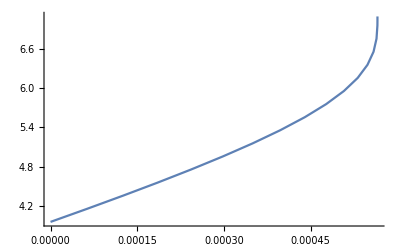

```mathematica
ListLinePlot[results[[;;,{1,2}]]]
```

```mathematica
f[x_]:=s[G[x]]^2;
Df[x_]:=Dtf[G[x]]k/s[G[x]];
eq1/.{G'[x]->(k G[x])/(q x s[G[x]])}//FullSimplify
eq2/.{G'[x]->(k G[x])/(q x s[G[x]])}//FullSimplify
eq3/.{G'[x]->(k G[x])/(q x s[G[x]]),G''[x]->-(k G[x] (-k s[G[x]]+q s[G[x]]^2+k G[x] s'[G[x]]))/(q^2 x^2 s[G[x]]^3)}//FullSimplify
eq4/.{G'[x]->(k G[x])/(q x s[G[x]]),G''[x]->-(k G[x] (-k s[G[x]]+q s[G[x]]^2+k G[x] s'[G[x]]))/(q^2 x^2 s[G[x]]^3)}//FullSimplify
```

k (-432+432 Dtf[G[x]]^2-G[x] (30 G[x]+G[x]^3+108 Dtf'[G[x]])-(6 Dtf[G[x]] G[x] (G[x] s[G[x]]+18 s'[G[x]]))/s[G[x]])==0

(k G[x] (s[G[x]] (-18 (-3+Dtf[G[x]]) G[x]+G[x]^3-324 Dtf'[G[x]])+324 Dtf[G[x]] s'[G[x]]))/(q x s[G[x]])==0

k G[x] (36-36 Dtf[G[x]]+2 G[x]^2+(9 G[x] s'[G[x]])/s[G[x]])==0

k G[x] (36-36 Dtf[G[x]]+2 G[x]^2+(9 G[x] s'[G[x]])/s[G[x]])==0

```mathematica
D[(k G[x])/(q x s[G[x]]),x]/.{G'[x]->(k G[x])/(q x s[G[x]])}//FullSimplify
```

-(k G[x] (-k s[G[x]]+q s[G[x]]^2+k G[x] s'[G[x]]))/(q^2 x^2 s[G[x]]^3)

```mathematica
DSolve[36-36 Dtf[G]+2 G^2+(9 G s'[G])/s[G]==0,s[G],G]
Solve[36-36 Dtf[G]+2 G^2+(9 G s'[G])/s[G]==0,s'[G],G]
```

{{s[G]→ⅇ^(∫_1^G -(2 (18-18 Dtf[K[1]]+K[1]^2))/(9 K[1])ⅆK[1]) C[1]}}

{{s'[G]→-(2 (18+G^2-18 Dtf[G]) s[G])/(9 G)}}

```mathematica
eq1//.{G'[x]->(k G[x])/(q x s[G[x]]),s'[G[x]]->-(2 (18+G[x]^2-18 Dtf[G[x]]) s[G[x]])/(9 G[x])}//FullSimplify
eq2//.{G'[x]->(k G[x])/(q x s[G[x]]),s'[G[x]]->-(2 (18+G[x]^2-18 Dtf[G[x]]) s[G[x]])/(9 G[x])}//FullSimplify
```

k (432+30 G[x]^2+G[x]^4-18 Dtf[G[x]] (24+G[x]^2)+108 G[x] Dtf'[G[x]])==0

(k (1296 Dtf[G[x]]^2-18 Dtf[G[x]] (72+5 G[x]^2)+G[x] (54 G[x]+G[x]^3-324 Dtf'[G[x]])))/(q x s[G[x]])==0

```mathematica
DSolve[432+30 G^2+G^4-18 Dtf[G] (24+G^2)+108 G Dtf'[G]==0,Dtf[G],G]//FullSimplify
DSolve[1296 Dtf[G]^2-18 Dtf[G] (72+5 G^2)+G (54 G+G^3-324 Dtf'[G])==0,Dtf[G],G]//FullSimplify
1296 Dtf[G]^2-18 Dtf[G] (72+5 G^2)+G (54 G+G^3-324 Dtf'[G])==0/.Solve[432+30 G^2+G^4-18 Dtf[G] (24+G^2)+108 G Dtf'[G]==0,Dtf'[G],G]//FullSimplify
```

{{Dtf[G]→1+G^2/18+ⅇ^(G^2/12) G^4 C[1]}}

{{Dtf[G]→(3 ⅇ^(G^2/12) (-864+24 G^2+G^4)+2 (18+G^2) C[1])/(36 (6 ⅇ^(G^2/12) (-12+G^2)+C[1]))}}

{18+G^2==18 Dtf[G]}

```mathematica
Dtf[G_]:=1+G^2/18;
432+30 G^2+G^4-18 Dtf[G] (24+G^2)+108 G Dtf'[G]==0//FullSimplify
1296 Dtf[G]^2-18 Dtf[G] (72+5 G^2)+G (54 G+G^3-324 Dtf'[G])==0//FullSimplify
-(2 (18-18 Dtf[K[1]]+K[1]^2))/(9 K[1])//FullSimplify
```

True

True

0

```mathematica
Everything above this line is a dead-end.
```

```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
```

```mathematica
Vtm12k2[ϕ_,G_]:=k^2 E^(2 ϕ/√6)(-12+4 √6 ϕ-3/2 ϕ^2+(√6)/4 ϕ G^2-3/2 G^2-1/16 G^4);
D[Vtm12k2[ϕ,G],G]==k^2 E^(2 ϕ/√6)((√6)/2 ϕ G-3G-1/4 G^3)//FullSimplify;
D[Vtm12k2[ϕ,G],ϕ]==k^2 E^(2 ϕ/√6)(5ϕ-(√6)/2 ϕ^2+1/2 ϕ G^2-(√6)/4 G^2-(√6)/48 G^4)//FullSimplify;
Vtm12k2scaled[ϕ_,G_]:=k^2(-12+4 √6 ϕ-3/2 ϕ^2+(√6)/4 ϕ G^2-3/2 G^2-1/16 G^4);
dVtdGscaled[ϕ_,G_]:=k^2((√6)/2 ϕ G-3G-1/4 G^3);
dVtdϕscaled[ϕ_,G_]:=k^2(5ϕ-(√6)/2 ϕ^2+1/2 ϕ G^2-(√6)/4 G^2-(√6)/48 G^4);
```

```mathematica
eq1=3 q (h[G]f'[G]Df[G]+f[G](a Df[G] h[G]ϕ'[G]+h[G]Df'[G]))-12f[G] Df[G]^2==Vtm12k2scaled[ϕ[G],G]/.a->1/(√6)//FullSimplify
eq2=Df'[G]+a ϕ'[G]Df[G]==1/6 q h[G](ϕ'[G]^2+1)/.a->1/(√6)//FullSimplify
eq3=q^2 f[G](a h[G]^2 ϕ'[G]^2+h[G]^2 ϕ''[G]+h[G]h'[G]ϕ'[G])+q^2 h[G]^2 f'[G]ϕ'[G]-4q h[G]f[G] Df[G] ϕ'[G]==dVtdϕscaled[ϕ[G],G]/.a->1/(√6)//FullSimplify
eq4=q^2 f[G](a h[G]^2 ϕ'[G]+ h[G]h'[G])+q^2 h[G]^2 f'[G]-4q f[G] Df[G] h[G]==dVtdGscaled[ϕ[G],G]/.a->1/(√6)//FullSimplify
eq1[[1]]-eq1[[2]]//Expand
eq2[[1]]-eq2[[2]]//Expand
eq3[[1]]-eq3[[2]]//Expand
eq4[[1]]-eq4[[2]]//Expand
```

k^2 (192+24 G^2+G^4-4 √6 (16+G^2) ϕ[G]+24 ϕ[G]^2)+48 q f[G] h[G] Df'[G]+8 q Df[G] h[G] (6 f'[G]+√6 f[G] ϕ'[G])==192 Df[G]^2 f[G]

q h[G] (1+ϕ'[G]^2)==6 Df'[G]+√6 Df[G] ϕ'[G]

√6 G^2 (12+G^2) k^2+24 k^2 ϕ[G] (-10-G^2+√6 ϕ[G])+8 q h[G] (6 (-4 Df[G] f[G]+q h[G] f'[G]+q f[G] h'[G]) ϕ'[G]+√6 q f[G] h[G] ϕ'[G]^2+6 q f[G] h[G] ϕ''[G])==0

3 G k^2 (12+G^2-2 √6 ϕ[G])+2 q h[G] (6 q h[G] f'[G]+f[G] (-24 Df[G]+6 q h'[G]+√6 q h[G] ϕ'[G]))==0

192 k^2+24 G^2 k^2+G^4 k^2-192 Df[G]^2 f[G]-64 √6 k^2 ϕ[G]-4 √6 G^2 k^2 ϕ[G]+24 k^2 ϕ[G]^2+48 q f[G] h[G] Df'[G]+48 q Df[G] h[G] f'[G]+8 √6 q Df[G] f[G] h[G] ϕ'[G]

q h[G]-6 Df'[G]-√6 Df[G] ϕ'[G]+q h[G] ϕ'[G]^2

12 √6 G^2 k^2+√6 G^4 k^2-240 k^2 ϕ[G]-24 G^2 k^2 ϕ[G]+24 √6 k^2 ϕ[G]^2-192 q Df[G] f[G] h[G] ϕ'[G]+48 q^2 h[G]^2 f'[G] ϕ'[G]+48 q^2 f[G] h[G] h'[G] ϕ'[G]+8 √6 q^2 f[G] h[G]^2 ϕ'[G]^2+48 q^2 f[G] h[G]^2 ϕ''[G]

36 G k^2+3 G^3 k^2-48 q Df[G] f[G] h[G]-6 √6 G k^2 ϕ[G]+12 q^2 h[G]^2 f'[G]+12 q^2 f[G] h[G] h'[G]+2 √6 q^2 f[G] h[G]^2 ϕ'[G]

```mathematica
f[G_]:=s[G]^2;
Df[G_]:=Dft[G]/s[G];
h[G_]:=ht[G]/s[G];
s[G_]:=Exp[st[G]];
eq1//FullSimplify
eq2//FullSimplify
eq3//FullSimplify
eq4//FullSimplify
eq1[[1]]-eq1[[2]]//Expand
ⅇ^st[G](eq2[[1]]-eq2[[2]])//Expand
eq3[[1]]-eq3[[2]]//Expand
eq4[[1]]-eq4[[2]]//Expand
```

k^2 (192+24 G^2+G^4-4 √6 (16+G^2) ϕ[G]+24 ϕ[G]^2)+48 q ht[G] Dft'[G]+8 Dft[G] (-24 Dft[G]+q ht[G] (6 st'[G]+√6 ϕ'[G]))==0

ⅇ^(-st[G]) (-6 Dft'[G]+Dft[G] (6 st'[G]-√6 ϕ'[G])+q ht[G] (1+ϕ'[G]^2))==0

√6 G^2 (12+G^2) k^2+24 k^2 ϕ[G] (-10-G^2+√6 ϕ[G])+8 q ht[G] (6 (-4 Dft[G]+q (ht'[G]+ht[G] st'[G])) ϕ'[G]+√6 q ht[G] ϕ'[G]^2+6 q ht[G] ϕ''[G])==0

3 G k^2 (12+G^2-2 √6 ϕ[G])+2 q ht[G] (-24 Dft[G]+q (6 ht'[G]+ht[G] (6 st'[G]+√6 ϕ'[G])))==0

192 k^2+24 G^2 k^2+G^4 k^2-192 Dft[G]^2-64 √6 k^2 ϕ[G]-4 √6 G^2 k^2 ϕ[G]+24 k^2 ϕ[G]^2+48 q ht[G] Dft'[G]+48 q Dft[G] ht[G] st'[G]+8 √6 q Dft[G] ht[G] ϕ'[G]

q ht[G]-6 Dft'[G]+6 Dft[G] st'[G]-√6 Dft[G] ϕ'[G]+q ht[G] ϕ'[G]^2

12 √6 G^2 k^2+√6 G^4 k^2-240 k^2 ϕ[G]-24 G^2 k^2 ϕ[G]+24 √6 k^2 ϕ[G]^2-192 q Dft[G] ht[G] ϕ'[G]+48 q^2 ht[G] ht'[G] ϕ'[G]+48 q^2 ht[G]^2 st'[G] ϕ'[G]+8 √6 q^2 ht[G]^2 ϕ'[G]^2+48 q^2 ht[G]^2 ϕ''[G]

36 G k^2+3 G^3 k^2-48 q Dft[G] ht[G]-6 √6 G k^2 ϕ[G]+12 q^2 ht[G] ht'[G]+12 q^2 ht[G]^2 st'[G]+2 √6 q^2 ht[G]^2 ϕ'[G]

```mathematica
(eq3[[1]]-eq3[[2]])-4ϕ'[G](eq4[[1]]-eq4[[2]])//Expand
```

12 √6 G^2 k^2+√6 G^4 k^2-240 k^2 ϕ[G]-24 G^2 k^2 ϕ[G]+24 √6 k^2 ϕ[G]^2-144 G k^2 ϕ'[G]-12 G^3 k^2 ϕ'[G]+24 √6 G k^2 ϕ[G] ϕ'[G]+48 q^2 f[G] h[G]^2 ϕ''[G]

```mathematica
DSolve[12 √6 G^2 k^2+√6 G^4 k^2-240 k^2 ϕ[G]-24 G^2 k^2 ϕ[G]+24 √6 k^2 ϕ[G]^2-144 G k^2 ϕ'[G]-12 G^3 k^2 ϕ'[G]+(0)24 √6 G k^2 ϕ[G] ϕ'[G]==Q[G],ϕ[G],G]
```

$Aborted

```mathematica
eq1[[1]]-eq1[[2]]//Expand
8q ht[G] ⅇ^st[G](eq2[[1]]-eq2[[2]])//Expand
(eq1[[1]]-eq1[[2]]-8q ht[G] ⅇ^st[G](eq2[[1]]-eq2[[2]]))//Expand
(4Dft[G])/(q ht[G])(eq4[[1]]-eq4[[2]])-8q ht[G] ⅇ^st[G](eq2[[1]]-eq2[[2]])//Expand
```

192 k^2+24 G^2 k^2+G^4 k^2-192 Dft[G]^2-64 √6 k^2 ϕ[G]-4 √6 G^2 k^2 ϕ[G]+24 k^2 ϕ[G]^2+48 q ht[G] Dft'[G]+48 q Dft[G] ht[G] st'[G]+8 √6 q Dft[G] ht[G] ϕ'[G]

8 q^2 ht[G]^2-48 q ht[G] Dft'[G]+48 q Dft[G] ht[G] st'[G]-8 √6 q Dft[G] ht[G] ϕ'[G]+8 q^2 ht[G]^2 ϕ'[G]^2

192 k^2+24 G^2 k^2+G^4 k^2-192 Dft[G]^2-8 q^2 ht[G]^2-64 √6 k^2 ϕ[G]-4 √6 G^2 k^2 ϕ[G]+24 k^2 ϕ[G]^2+96 q ht[G] Dft'[G]+16 √6 q Dft[G] ht[G] ϕ'[G]-8 q^2 ht[G]^2 ϕ'[G]^2

-192 Dft[G]^2+(144 G k^2 Dft[G])/(q ht[G])+(12 G^3 k^2 Dft[G])/(q ht[G])-8 q^2 ht[G]^2-(24 √6 G k^2 Dft[G] ϕ[G])/(q ht[G])+48 q ht[G] Dft'[G]+48 q Dft[G] ht'[G]+16 √6 q Dft[G] ht[G] ϕ'[G]-8 q^2 ht[G]^2 ϕ'[G]^2

```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
```

```mathematica
Vtm12k2[ϕ_,G_]:=k^2 E^(2 ϕ/√6)(-12+4 √6 ϕ-3/2 ϕ^2+(√6)/4 ϕ G^2-3/2 G^2-1/16 G^4);
D[Vtm12k2[ϕ,G],G]==k^2 E^(2 ϕ/√6)((√6)/2 ϕ G-3G-1/4 G^3)//FullSimplify;
D[Vtm12k2[ϕ,G],ϕ]==k^2 E^(2 ϕ/√6)(5ϕ-(√6)/2 ϕ^2+1/2 ϕ G^2-(√6)/4 G^2-(√6)/48 G^4)//FullSimplify;
Vtm12k2scaled[ϕ_,G_]:=k^2(-12+4 √6 ϕ-3/2 ϕ^2+(√6)/4 ϕ G^2-3/2 G^2-1/16 G^4);
dVtdGscaled[ϕ_,G_]:=k^2((√6)/2 ϕ G-3G-1/4 G^3);
dVtdϕscaled[ϕ_,G_]:=k^2(5ϕ-(√6)/2 ϕ^2+1/2 ϕ G^2-(√6)/4 G^2-(√6)/48 G^4);
```

```mathematica
eq1=3 q w[ϕ](f'[ϕ]Df[ϕ]+f[ϕ](a Df[ϕ]+Df'[ϕ]))-12f[ϕ] Df[ϕ]^2==Vtm12k2scaled[ϕ,G[ϕ]]/.a->1/(√6)//FullSimplify
eq2=Df'[ϕ]+a Df[ϕ]==1/6 q w[ϕ](1+G'[ϕ]^2)/.a->1/(√6)//FullSimplify
eq3=q^2 f[ϕ](a w[ϕ]^2+w[ϕ]w'[ϕ])+q^2 w[ϕ]^2 f'[ϕ]-4q f[ϕ] Df[ϕ] w[ϕ]==dVtdϕscaled[ϕ,G[ϕ]]/.a->1/(√6)//FullSimplify
eq4=q^2 f[ϕ](a w[ϕ]^2 G'[ϕ]+w[ϕ]^2 G''[ϕ]+w[ϕ]w'[ϕ]G'[ϕ])+q^2 w[ϕ]^2 f'[ϕ]G'[ϕ]-4q w[ϕ]f[ϕ] Df[ϕ] G'[ϕ]==dVtdGscaled[ϕ,G[ϕ]]/.a->1/(√6)//FullSimplify
eq1[[1]]-eq1[[2]]//Expand
eq2[[1]]-eq2[[2]]//Expand
eq3[[1]]-eq3[[2]]//Expand
eq4[[1]]-eq4[[2]]//Expand
```

1/16 k^2 (192+24 ϕ^2+24 G[ϕ]^2+G[ϕ]^4-4 √6 ϕ (16+G[ϕ]^2))+3 q w[ϕ] (f[ϕ] Df'[ϕ]+Df[ϕ] (f[ϕ]/(√6)+f'[ϕ]))==12 Df[ϕ]^2 f[ϕ]

√6 Df[ϕ]+6 Df'[ϕ]==q w[ϕ] (1+G'[ϕ]^2)

k^2 (24 ϕ (-10+√6 ϕ)+G[ϕ]^2 (-24 ϕ+√6 (12+G[ϕ]^2)))+8 q w[ϕ] (-24 Df[ϕ] f[ϕ]+q (6 w[ϕ] f'[ϕ]+f[ϕ] (√6 w[ϕ]+6 w'[ϕ])))==0

3 k^2 G[ϕ] (12-2 √6 ϕ+G[ϕ]^2)+2 q w[ϕ] (G'[ϕ] (-24 Df[ϕ] f[ϕ]+q (6 w[ϕ] f'[ϕ]+f[ϕ] (√6 w[ϕ]+6 w'[ϕ])))+6 q f[ϕ] w[ϕ] G''[ϕ])==0

12 k^2-4 √6 k^2 ϕ+(3 k^2 ϕ^2)/2-12 Df[ϕ]^2 f[ϕ]+3/2 k^2 G[ϕ]^2-1/2 √(3/2) k^2 ϕ G[ϕ]^2+1/16 k^2 G[ϕ]^4+√(3/2) q Df[ϕ] f[ϕ] w[ϕ]+3 q f[ϕ] w[ϕ] Df'[ϕ]+3 q Df[ϕ] w[ϕ] f'[ϕ]

√6 Df[ϕ]-q w[ϕ]+6 Df'[ϕ]-q w[ϕ] G'[ϕ]^2

-240 k^2 ϕ+24 √6 k^2 ϕ^2+12 √6 k^2 G[ϕ]^2-24 k^2 ϕ G[ϕ]^2+√6 k^2 G[ϕ]^4-192 q Df[ϕ] f[ϕ] w[ϕ]+8 √6 q^2 f[ϕ] w[ϕ]^2+48 q^2 w[ϕ]^2 f'[ϕ]+48 q^2 f[ϕ] w[ϕ] w'[ϕ]

36 k^2 G[ϕ]-6 √6 k^2 ϕ G[ϕ]+3 k^2 G[ϕ]^3-48 q Df[ϕ] f[ϕ] w[ϕ] G'[ϕ]+2 √6 q^2 f[ϕ] w[ϕ]^2 G'[ϕ]+12 q^2 w[ϕ]^2 f'[ϕ] G'[ϕ]+12 q^2 f[ϕ] w[ϕ] G'[ϕ] w'[ϕ]+12 q^2 f[ϕ] w[ϕ]^2 G''[ϕ]

```mathematica
Df[ϕ_]:=E^(-ϕ/√6)Dft[ϕ];
w[ϕ_]:=E^(-ϕ/√6)wt[ϕ];
eq1//FullSimplify
eq2//FullSimplify
```

k^2 (-192-24 ϕ^2-24 G[ϕ]^2-G[ϕ]^4+4 √6 ϕ (16+G[ϕ]^2))==48 ⅇ^(-√(2/3) ϕ) (-4 Dft[ϕ]^2 f[ϕ]+q f[ϕ] wt[ϕ] Dft'[ϕ]+q Dft[ϕ] wt[ϕ] f'[ϕ])

ⅇ^(-ϕ/(√6)) (-6 Dft'[ϕ]+q wt[ϕ] (1+G'[ϕ]^2))==0

```mathematica
DSolve[eq2,Dft[ϕ],ϕ]//FullSimplify
DSolve[eq1/.Solve[eq2,Dft'[ϕ]],f[ϕ],ϕ]//FullSimplify
```

{{Dft[ϕ]→C[1]+∫_1^ϕ 1/6 q wt[K[1]] (1+G'[K[1]]^2)ⅆK[1]}}

{{f[ϕ]→ⅇ^(∫_1^ϕ (24 Dft[K[1]]^2-q^2 wt[K[1]]^2 (1+G'[K[1]]^2))/(6 q Dft[K[1]] wt[K[1]])ⅆK[1]) (C[1]+∫_1^ϕ -(ⅇ^(-∫_1^K[2] (24 Dft[K[1]]^2-q^2 wt[K[1]]^2 (1+G'[K[1]]^2))/(6 q Dft[K[1]] wt[K[1]])ⅆK[1]+√(2/3) K[2]) k^2 (G[K[2]]^4-4 G[K[2]]^2 (-6+√6 K[2])+8 (24-8 √6 K[2]+3 K[2]^2)))/(48 q Dft[K[2]] wt[K[2]])ⅆK[2])}}

```mathematica
f[ϕ_]:=s[ϕ]^2;
Df[ϕ_]:=Dft[ϕ]/s[ϕ];
w[ϕ_]:=wt[ϕ]/s[ϕ];
s[ϕ_]:=Exp[st[ϕ]];
eq3[[1]]-eq3[[2]]//Expand
eq4[[1]]-eq4[[2]]//Expand
eq5=0==4(eq4[[1]]-eq4[[2]])-G'[ϕ](eq3[[1]]-eq3[[2]])//Expand
```

-240 k^2 ϕ+24 √6 k^2 ϕ^2+12 √6 k^2 G[ϕ]^2-24 k^2 ϕ G[ϕ]^2+√6 k^2 G[ϕ]^4-192 q Dft[ϕ] wt[ϕ]+8 √6 q^2 wt[ϕ]^2+48 q^2 wt[ϕ]^2 st'[ϕ]+48 q^2 wt[ϕ] wt'[ϕ]

36 k^2 G[ϕ]-6 √6 k^2 ϕ G[ϕ]+3 k^2 G[ϕ]^3-48 q Dft[ϕ] wt[ϕ] G'[ϕ]+2 √6 q^2 wt[ϕ]^2 G'[ϕ]+12 q^2 wt[ϕ]^2 G'[ϕ] st'[ϕ]+12 q^2 wt[ϕ] G'[ϕ] wt'[ϕ]+12 q^2 wt[ϕ]^2 G''[ϕ]

0==144 k^2 G[ϕ]-24 √6 k^2 ϕ G[ϕ]+12 k^2 G[ϕ]^3+240 k^2 ϕ G'[ϕ]-24 √6 k^2 ϕ^2 G'[ϕ]-12 √6 k^2 G[ϕ]^2 G'[ϕ]+24 k^2 ϕ G[ϕ]^2 G'[ϕ]-√6 k^2 G[ϕ]^4 G'[ϕ]+48 q^2 wt[ϕ]^2 G''[ϕ]

```mathematica
Module[{G},
G[ϕ_]:=a[ϕ]Gt[ϕ];
Coefficient[144 k^2 G[ϕ]-24 √6 k^2 ϕ G[ϕ]+12 k^2 G[ϕ]^3+240 k^2 ϕ G'[ϕ]-24 √6 k^2 ϕ^2 G'[ϕ]-12 √6 k^2 G[ϕ]^2 G'[ϕ]+24 k^2 ϕ G[ϕ]^2 G'[ϕ]-√6 k^2 G[ϕ]^4 G'[ϕ]+48 q^2 wt[ϕ]^2 G''[ϕ]//Expand,Gt'[ϕ]]
]
DSolve[240 k^2 ϕ a[ϕ]-24 √6 k^2 ϕ^2 a[ϕ]-12 √6 k^2 a[ϕ]^3 Gt[ϕ]^2+24 k^2 ϕ a[ϕ]^3 Gt[ϕ]^2-√6 k^2 a[ϕ]^5 Gt[ϕ]^4+96 q^2 wt[ϕ]^2 a'[ϕ]==0,a[ϕ],ϕ]
```

240 k^2 ϕ a[ϕ]-24 √6 k^2 ϕ^2 a[ϕ]-12 √6 k^2 a[ϕ]^3 Gt[ϕ]^2+24 k^2 ϕ a[ϕ]^3 Gt[ϕ]^2-√6 k^2 a[ϕ]^5 Gt[ϕ]^4+96 q^2 wt[ϕ]^2 a'[ϕ]

DSolve[240 k^2 ϕ a[ϕ]-24 √6 k^2 ϕ^2 a[ϕ]-12 √6 k^2 a[ϕ]^3 Gt[ϕ]^2+24 k^2 ϕ a[ϕ]^3 Gt[ϕ]^2-√6 k^2 a[ϕ]^5 Gt[ϕ]^4+96 q^2 wt[ϕ]^2 a'[ϕ]==0,a[ϕ],ϕ]

```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
```

```mathematica
Vtm12k2[ϕ_,G_]:=k^2 E^(2 ϕ/√6)(-12+4 √6 ϕ-3/2 ϕ^2+(√6)/4 ϕ G^2-3/2 G^2-1/16 G^4);
D[Vtm12k2[ϕ,G],G]==k^2 E^(2 ϕ/√6)((√6)/2 ϕ G-3G-1/4 G^3)//FullSimplify;
D[Vtm12k2[ϕ,G],ϕ]==k^2 E^(2 ϕ/√6)(5ϕ-(√6)/2 ϕ^2+1/2 ϕ G^2-(√6)/4 G^2-(√6)/48 G^4)//FullSimplify;
Vtm12k2scaled[ϕ_,G_]:=k^2(-12+4 √6 ϕ-3/2 ϕ^2+(√6)/4 ϕ G^2-3/2 G^2-1/16 G^4);
dVtdGscaled[ϕ_,G_]:=k^2((√6)/2 ϕ G-3G-1/4 G^3);
dVtdϕscaled[ϕ_,G_]:=k^2(5ϕ-(√6)/2 ϕ^2+1/2 ϕ G^2-(√6)/4 G^2-(√6)/48 G^4);
```

```mathematica
B[ϕ_,G_]:=E^(ϕ/√6)Bt[ϕ,G]-q;
Bt[ϕ_,G_]:=Exp[Bϕ[ϕ]+BG[G]];
f[ϕ_,G_]:=Exp[fϕ[ϕ]+fG[G]];
Bt[ϕ_,G_]:=Bϕ[ϕ]BG[G];
f[ϕ_,G_]:=fϕ[ϕ]fG[G];
eq1=18(D[B[ϕ,G], ϕ]D[f[ϕ,G], ϕ]+D[B[ϕ,G], G]D[f[ϕ,G], G])(B[ϕ,G]+q)+18f[ϕ,G]((D[B[ϕ,G], ϕ])^2+(D[B[ϕ,G], G])^2)-12f[ϕ,G](B[ϕ,G]+q)^2==Vtm12k2[ϕ,G]//FullSimplify
eq2=D[B[ϕ,G], ϕ]D[(D[B[ϕ,G], ϕ]D[f[ϕ,G], ϕ]+D[B[ϕ,G], G]D[f[ϕ,G], G]), ϕ]+D[B[ϕ,G], G]D[(D[B[ϕ,G], ϕ]D[f[ϕ,G], ϕ]+D[B[ϕ,G], G]D[f[ϕ,G], G]), G]==2/3(B[ϕ,G]+q)(D[B[ϕ,G], ϕ]D[f[ϕ,G], ϕ]+D[B[ϕ,G], G]D[f[ϕ,G], G])//FullSimplify
```

ⅇ^(√(2/3) ϕ) (-k^2 (192+24 G^2+G^4-4 √6 (16+G^2) ϕ+24 ϕ^2)-288 Bϕ[ϕ]^2 fG[G] fϕ[ϕ] BG'[G]^2-288 BG[G] Bϕ[ϕ]^2 fϕ[ϕ] BG'[G] fG'[G]+48 BG[G]^2 fG[G] (-6 fϕ[ϕ] Bϕ'[ϕ]^2-2 Bϕ[ϕ] Bϕ'[ϕ] (√6 fϕ[ϕ]+3 fϕ'[ϕ])+Bϕ[ϕ]^2 (3 fϕ[ϕ]-√6 fϕ'[ϕ])))==0

ⅇ^(√(2/3) ϕ) (-2 BG[G] BG'[G] fG'[G] (6 fϕ[ϕ] Bϕ'[ϕ]^2+2 Bϕ[ϕ] Bϕ'[ϕ] (√6 fϕ[ϕ]+6 fϕ'[ϕ])+Bϕ[ϕ]^2 (-3 fϕ[ϕ]+2 √6 fϕ'[ϕ]))+2 Bϕ[ϕ] BG'[G] (-fG[G] BG'[G] (√6 Bϕ[ϕ]+6 Bϕ'[ϕ]) fϕ'[ϕ]-6 Bϕ[ϕ] fϕ[ϕ] (fG'[G] BG''[G]+BG'[G] fG''[G]))+BG[G]^2 fG[G] (Bϕ[ϕ]^2 (√6 fϕ'[ϕ]-2 fϕ''[ϕ])-4 Bϕ'[ϕ] (3 fϕ'[ϕ] Bϕ''[ϕ]+Bϕ'[ϕ] (√6 fϕ'[ϕ]+3 fϕ''[ϕ]))+2 Bϕ[ϕ] (-√6 fϕ'[ϕ] Bϕ''[ϕ]+Bϕ'[ϕ] (fϕ'[ϕ]-2 √6 fϕ''[ϕ]))))==0

```mathematica
(Bt[ϕ,G](eq2[[1]]-eq2[[2]]))/(f[ϕ,G](B[ϕ,G]+q)^2)//Expand
```

(6 Bϕ[ϕ] BG'[G] fG'[G])/fG[G]-(4 √6 BG'[G] Bϕ'[ϕ] fG'[G])/fG[G]-(12 BG'[G] Bϕ'[ϕ]^2 fG'[G])/(Bϕ[ϕ] fG[G])+(√6 BG[G] Bϕ[ϕ] fϕ'[ϕ])/fϕ[ϕ]-(2 √6 Bϕ[ϕ] BG'[G]^2 fϕ'[ϕ])/(BG[G] fϕ[ϕ])+(2 BG[G] Bϕ'[ϕ] fϕ'[ϕ])/fϕ[ϕ]-(12 BG'[G]^2 Bϕ'[ϕ] fϕ'[ϕ])/(BG[G] fϕ[ϕ])-(4 √6 BG[G] Bϕ'[ϕ]^2 fϕ'[ϕ])/(Bϕ[ϕ] fϕ[ϕ])-(4 √6 Bϕ[ϕ] BG'[G] fG'[G] fϕ'[ϕ])/(fG[G] fϕ[ϕ])-(24 BG'[G] Bϕ'[ϕ] fG'[G] fϕ'[ϕ])/(fG[G] fϕ[ϕ])-(12 Bϕ[ϕ] BG'[G] fG'[G] BG''[G])/(BG[G] fG[G])-(2 √6 BG[G] fϕ'[ϕ] Bϕ''[ϕ])/fϕ[ϕ]-(12 BG[G] Bϕ'[ϕ] fϕ'[ϕ] Bϕ''[ϕ])/(Bϕ[ϕ] fϕ[ϕ])-(12 Bϕ[ϕ] BG'[G]^2 fG''[G])/(BG[G] fG[G])-(2 BG[G] Bϕ[ϕ] fϕ''[ϕ])/fϕ[ϕ]-(4 √6 BG[G] Bϕ'[ϕ] fϕ''[ϕ])/fϕ[ϕ]-(12 BG[G] Bϕ'[ϕ]^2 fϕ''[ϕ])/(Bϕ[ϕ] fϕ[ϕ])

```mathematica
D[E^q[x],{x,2}]
```

ⅇ^q[x] q'[x]^2+ⅇ^q[x] q''[x]

```mathematica
DSolve[f''[y]==4(B[y]+q)f'[y],f[y],y]
D[C[2]+∫_1^y ⅇ^(∫_1^K[2] 4 (q+B[K[1]])ⅆK[1]) C[1]ⅆK[2],{y,1}]//FullSimplify
D[C[2]+∫_1^y ⅇ^(∫_1^K[2] 4 (q+B[K[1]])ⅆK[1]) C[1]ⅆK[2],{y,2}]//FullSimplify
```

{{f[y]→C[2]+∫_1^y ⅇ^(∫_1^K[2] 4 (q+B[K[1]])ⅆK[1]) C[1]ⅆK[2]}}

ⅇ^(∫_1^y 4 (q+B[K[1]])ⅆK[1]) C[1]

4 ⅇ^(∫_1^y 4 (q+B[K[1]])ⅆK[1]) (q+B[y]) C[1]

```mathematica
newEq=3(f'[y](B[y]+q)+f[y]B'[y])-12f[y](B[y]+q)^2==k^2 E^(2 ϕ[y]/√6)(-12+4 √6 ϕ[y]-3/2 ϕ[y]^2+(√6)/4 ϕ[y] G[y]^2-3/2 G[y]^2-1/16 G[y]^4)/.{f[y]->C[2]+∫_1^y ⅇ^(∫_1^K[2] 4 (q+B[K[1]])ⅆK[1]) C[1]ⅆK[2],f'[y]->ⅇ^(∫_1^y 4 (q+B[K[1]])ⅆK[1]) C[1]}//FullSimplify
```

3 ⅇ^(∫_1^y 4 (q+B[K[1]])ⅆK[1]) (q+B[y]) C[1]==1/16 ⅇ^(√(2/3) ϕ[y]) k^2 (-G[y]^4+4 G[y]^2 (-6+√6 ϕ[y])+8 (-24+8 √6 ϕ[y]-3 ϕ[y]^2))+3 (C[2]+∫_1^y ⅇ^(∫_1^K[2] 4 (q+B[K[1]])ⅆK[1]) C[1]ⅆK[2]) (4 (q+B[y])^2-B'[y])